Settings

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

Lengths

Unit conversion
1. From hat quantities to km: requires calculation of ω_m 
2. From km to hat quantities

How is thetam related omegam?
ω_m=ω_v √((λ/ω_v-cos^2(2 θ_v))^2+sin^2(2 θ_v)) 
=> ω_m/ω_v=√(((sin 2 θ_v)/(tan 2 θ_m))^2+sin^2(2 θ_v))
and we know that 1 unit of ω_v is usally 10km scale (SHOULD DO A CALCULATION HERE)

```mathematica
ThetaMatter[thetav_,lambda_,omegav_:1]:=ArcTan[Sin[2thetav]/(Cos[2thetav]-lambda/omegav)]/2;
```

```mathematica
OmegaMatter[thetam_,thetav_,omegav_:1]:=omegav*Sqrt[Sin[thetav]^2+(Sin[2thetav]/Tan[2thetam])^2];
```

```mathematica
OmegaMatter2[lambda_,thetav_,omegav_:1]:=omegav*Sqrt[(lambda/omegav-Cos[2thetav])^2+Sin[2thetav]^2];
```

```mathematica
OmegaVacuum[energy_,deltam2_]:=deltam2/(2energy);(*input should be using the same units*)
```

```mathematica
MeVInverse2km[mev_]:=1.97*10^(-13)*(mev);(*  mev/1MeV=mev*(1/1MeV)=mev*(197fm)=...   *)
```

```mathematica
MeVInverse2km[1]
```

1.97×10^-13

Parameters

Vacuum parameters

```mathematica
gF=1.17*10^(-11)(*MeV^(-2)*)
ye=0.5
```

1.17×10^-11

0.5

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
OmegaVacuum[energy10,deltamsquare13];
```

```mathematica
omegaV=deltamsquare13/(2 energy10)(*MeV*);(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093/2];
```

As a reference, MSW resonance density is (for 10 MeV neutrinos)

```mathematica
mswDensity10=(deltamsquare13*Cos[2thetaV]/(2 √2 gF energy10))*1.3*10^(41)*10^(-9)*1.67*10^(-24)/ye (*g/cc*)
```

3252.77

```mathematica
fraction=20
lambdaN=fraction*Cos[2thetaV]omegaV
```

20

2.4791×10^-15

```mathematica
thetamN=ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2;(*Pi/6*)
phiN=0;
kN=0.9999;
aN=0.1*lambdaN/OmegaMatter[thetamN,thetaV,omegaV](*(kN)^(-5/3)*);
init={psi1[0],psi2[0]}=={1,0};
(*background potential BEGIN*)
kN0=0;
aN0=0;
(*background potential END*)
endpointN=endpointSolved/.First@Solve[MeVInverse2km[endpointSolved/OmegaMatter[thetamN,thetaV,omegaV]]==20000,endpointSolved]
```

4787.05

```mathematica
aN
```

0.00525762

Test the omega functions

```mathematica
OmegaMatter[thetamN,thetaV,omegaV]
OmegaMatter[thetamN,thetaV]
```

4.71525×10^-14

362.711

```mathematica
fun[khat_,ahat_,thetam_,n0_]=1/2 ahat Sin[2thetam](2n0)/zk BesselJ[n0,zk]/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]

```mathematica
amplitude[khat_,ahat_,thetam_,n0_] = ( Abs[fun[khat,ahat,thetam,n0]]^2)/( Abs[fun[khat,ahat,thetam,n0]]^2+(n0 khat - 1)^2)/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2/((-1+khat n0)^2+Abs[khat n0 BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2)

```mathematica
amplitude[kN,aN,thetamN,1]
```

0.000476928

```mathematica
amplitude[0.00001,aN0,thetamN,1]
```

0.

```mathematica
(*resonanceWidthVSBackgroundDensityTicks=Table[{frac*Cos[2thetaV]omegaV,ScientificForm[mswDensity10*frac,2]},{frac,0.1,10}]*)
resonanceWidthVSBackgroundDensityTicks=Table[{frac,ScientificForm[mswDensity10*frac,2]},{frac,0.1,10}]
```

{{0.1,3.3×10^2},{1.1,3.6×10^3},{2.1,6.8×10^3},{3.1,1.×10^4},{4.1,1.3×10^4},{5.1,1.7×10^4},{6.1,2.×10^4},{7.1,2.3×10^4},{8.1,2.6×10^4},{9.1,3.×10^4}}

```mathematica
(*LogPlot[{Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda/omegaV)^2)]/2,1],Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda/omegaV)^2)]/2,2]},{lambda,0.1Cos[2thetaV]omegaV,10Cos[2thetaV]omegaV},PlotRange->Full,ImageSize->imgsize*1.2,Frame->True,FrameLabel->{{"Width/ω_m",None},{"λ (MeV)","ρ (g/cm^3)"}},PlotLabel->"Resonance Width and Background Matter Density",FrameTicks->{{Automatic,Automatic},{Automatic,resonanceWidthVSBackgroundDensityTicks}},PlotLegends->Placed[{"n=1","n=2"},{Center,Above}],GridLines->{{{Cos[2thetaV]omegaV,Red}},Automatic},GridLinesStyle->Directive[LightGray, Dashed],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]*)
LogPlot[{Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(frac*Cos[2thetaV])^2)]/2,1],Abs@fun[1,aN,ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(frac*Cos[2thetaV])^2)]/2,2]},{frac,0.1,10},PlotRange->Full,ImageSize->imgsize*1.2,Frame->True,FrameLabel->{{"Width/ω_m",None},{"λ/λ_msw","ρ (g/cm^3)"}},PlotLabel->"Resonance Width and Background Matter Density",FrameTicks->{{Automatic,Automatic},{Automatic,resonanceWidthVSBackgroundDensityTicks}},PlotLegends->Placed[{"n=1","n=2"},{Center,Above}],GridLines->{{{1,Red}},Automatic},GridLinesStyle->Directive[LightGray, Dashed],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

```mathematica
qFreq[k_,a_,thetam_,n_]:=Sqrt[fun[k,a,thetam,n]^2+(n k - 1)^2]
```

```mathematica
qFreqTicksFullk=Table[{k,ScientificForm[MeVInverse2km[1/(k*OmegaMatter[thetamN,thetaV,omegaV])],2]},{k,1,5}]
```

{{1,4.2},{2,2.1},{3,1.4},{4,1.},{5,8.4×10^-1}}

```mathematica
qFreqTicksFullq=Table[{q,ScientificForm[MeVInverse2km[1/(q*OmegaMatter[thetamN,thetaV,omegaV])],2]},{q,qFreq[1,aN,thetamN,1],qFreq[5,aN,thetamN,1],0.5}]
```

{{2.18439×10^-6,1.9×10^6},{0.500002,8.4},{1.,4.2},{1.5,2.8},{2.,2.1},{2.5,1.7},{3.,1.4},{3.5,1.2}}

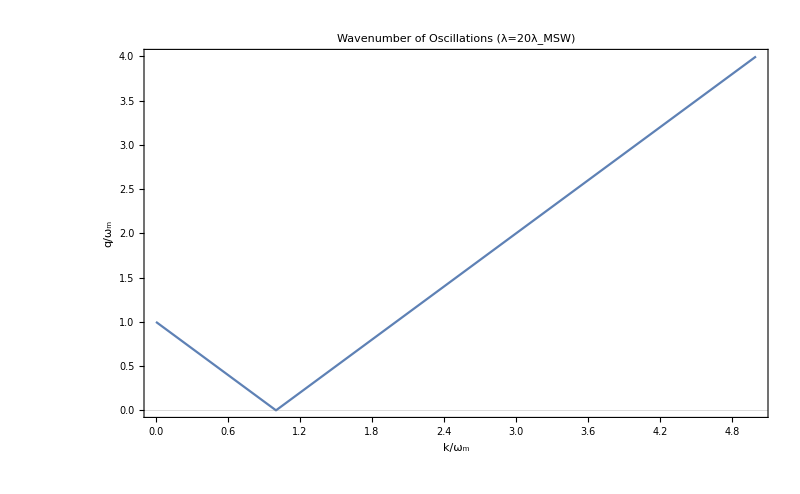

```mathematica
Plot[qFreq[k,aN,thetamN,1],{k,0,5},Frame->True,ImageSize->imgsize,PlotLabel->"Wavenumber of Oscillations (λ="<>ToString[fraction]<>"λ_MSW)",FrameLabel->{{"q/ω_m","Oscillation Wavelength (km)"},{"k/ω_m","Perturbation Wavelength (km)"}},FrameTicks->{{Automatic,qFreqTicksFullq},{Automatic,qFreqTicksFullk}},GridLines->{None,{qFreq[1,aN,thetamN,1]}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

```mathematica
probApprox[x_,nN_]:=amplitude[kN,aN,thetamN,nN](Sin[Sqrt[ Abs[fun[kN,aN,thetamN,nN]]^2+(nN kN - 1)^2]x/2])^2;
```

```mathematica
pltProbApprox=Plot[probApprox[x,1],{x,0,endpointN},PlotStyle->Blue,Frame->True,ImageSize->imgsize,PlotLabel->"Stimulated Oscillations with Approximation",PlotLegends->Placed[{Style["Approximation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

```mathematica
hN[x_]:=(aN Sin[kN x+phiN])Sin[2thetamN]Exp[I(-x-Cos[2thetamN] aN/kN Cos[kN x+phiN])]/2;
```

```mathematica
solN=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hN[x]},{Conjugate[hN[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointN},MaxSteps->10^6];

pltN=Plot[Evaluate[Abs[psi2[x]]^2/.solN],{x,0,endpointN},ImageSize->imgsize,Frame->True,FrameLabel->{"x̂","Transition Probability"},PlotStyle->{Red,Thickness[0.005],Dashing[{0.004,0.03}]},PlotLabel->"Stimulated Oscillations",PlotLegends->Placed[{Style["Numerical Calculation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

```mathematica
Show[pltProbApprox,pltN,FrameLabel->{"x̂","Transition Probability"},PlotLabel->"Stimulated Oscillations",LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
```

-Graphics-

Remake Graph Using km

```mathematica
OmegaMatter[thetamN,thetaV,omegaV]
```

4.71525×10^-14

```mathematica
pltProbApproxTicksFull=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamN,thetaV,omegaV]],2]},{x,0,endpointN}];
```

```mathematica
pltProbApproxTicks=Take[pltProbApproxTicksFull,{1,Length@pltProbApproxTicksFull,Floor[(Length@pltProbApproxTicksFull)/5]}];
```

```mathematica
pltProbApproxTicks
```

{{0,0.},{957,4.×10^3},{1914,8.×10^3},{2871,1.2×10^4},{3828,1.6×10^4},{4785,2.×10^4}}

```mathematica
pltProbApprox2=Plot[probApprox[x,1],{x,0,endpointN},PlotStyle->Blue,Frame->True,ImageSize->imgsize,PlotLabel->"Stimulated Oscillations with Approximation",PlotLegends->Placed[{Style["Approximation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},FrameTicks->{{Automatic,None},{Automatic,pltProbApproxTicks}},FrameLabel->{{"Probability",None},{"x̂","Distance (km)"}}]
```

-Graphics-

```mathematica
Show[pltProbApprox2,pltN,PlotLabel->"Stimulated Oscillations (λ="<>ToString[fraction]<>"λ_MSw)"]
```

-Graphics-

The oscillation length of the matter profile

```mathematica
MeVInverse2km[kN/OmegaMatter[thetamN,thetaV,omegaV]](*km*)
```

4.17752

```mathematica
omegaV(√((OmegaMatter[thetamN,thetaV,omegaV]/omegaV)^2+Sin[2thetaV]^2)+Cos[2thetaV]^2)
```

4.72707×10^-14

Matter profile used here is

```mathematica
endpointNMatterProfile=Floor@endpointN/10
```

4787/10

```mathematica
frameTicksMatterProfile=Take[Table[{x,MeVInverse2km[x/OmegaMatter[thetamN,thetaV,omegaV]]},{x,0,endpointNMatterProfile}],{1,endpointNMatterProfile,Floor[(endpointNMatterProfile)/10]}]
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{0, 0.}, {1, 4.17793}, {2, 8.35587}, {3, 12.5338}, {4, 16.7117}, {5, 20.8897}, {6, 25.0676}, « 37 », {44, 183.829}, {45, 188.007}, {46, 192.185}, {47, 196.363}, {48, 200.541}, {49, 204.719}, « 429 »}, {1, 4787/10, 47}].

Take[{{0,0.},{1,4.17793},{2,8.35587},{3,12.5338},{4,16.7117},{5,20.8897},{6,25.0676},{7,29.2455},{8,33.4235},{9,37.6014},{10,41.7793},{11,45.9573},{12,50.1352},{13,54.3131},{14,58.4911},{15,62.669},{16,66.847},{17,71.0249},{18,75.2028},{19,79.3808},{20,83.5587},{21,87.7366},{22,91.9146},{23,96.0925},{24,100.27},{25,104.448},{26,108.626},{27,112.804},{28,116.982},{29,121.16},{30,125.338},{31,129.516},{32,133.694},{33,137.872},{34,142.05},{35,146.228},{36,150.406},{37,154.584},{38,158.762},{39,162.939},{40,167.117},{41,171.295},{42,175.473},{43,179.651},{44,183.829},{45,188.007},{46,192.185},{47,196.363},{48,200.541},{49,204.719},{50,208.897},{51,213.075},{52,217.253},{53,221.431},{54,225.608},{55,229.786},{56,233.964},{57,238.142},{58,242.32},{59,246.498},{60,250.676},{61,254.854},{62,259.032},{63,263.21},{64,267.388},{65,271.566},{66,275.744},{67,279.922},{68,284.1},{69,288.277},{70,292.455},{71,296.633},{72,300.811},{73,304.989},{74,309.167},{75,313.345},{76,317.523},{77,321.701},{78,325.879},{79,330.057},{80,334.235},{81,338.413},{82,342.591},{83,346.769},{84,350.947},{85,355.124},{86,359.302},{87,363.48},{88,367.658},{89,371.836},{90,376.014},{91,380.192},{92,384.37},{93,388.548},{94,392.726},{95,396.904},{96,401.082},{97,405.26},{98,409.438},{99,413.616},{100,417.793},{101,421.971},{102,426.149},{103,430.327},{104,434.505},{105,438.683},{106,442.861},{107,447.039},{108,451.217},{109,455.395},{110,459.573},{111,463.751},{112,467.929},{113,472.107},{114,476.285},{115,480.462},{116,484.64},{117,488.818},{118,492.996},{119,497.174},{120,501.352},{121,505.53},{122,509.708},{123,513.886},{124,518.064},{125,522.242},{126,526.42},{127,530.598},{128,534.776},{129,538.954},{130,543.131},{131,547.309},{132,551.487},{133,555.665},{134,559.843},{135,564.021},{136,568.199},{137,572.377},{138,576.555},{139,580.733},{140,584.911},{141,589.089},{142,593.267},{143,597.445},{144,601.623},{145,605.801},{146,609.978},{147,614.156},{148,618.334},{149,622.512},{150,626.69},{151,630.868},{152,635.046},{153,639.224},{154,643.402},{155,647.58},{156,651.758},{157,655.936},{158,660.114},{159,664.292},{160,668.47},{161,672.647},{162,676.825},{163,681.003},{164,685.181},{165,689.359},{166,693.537},{167,697.715},{168,701.893},{169,706.071},{170,710.249},{171,714.427},{172,718.605},{173,722.783},{174,726.961},{175,731.139},{176,735.316},{177,739.494},{178,743.672},{179,747.85},{180,752.028},{181,756.206},{182,760.384},{183,764.562},{184,768.74},{185,772.918},{186,777.096},{187,781.274},{188,785.452},{189,789.63},{190,793.808},{191,797.985},{192,802.163},{193,806.341},{194,810.519},{195,814.697},{196,818.875},{197,823.053},{198,827.231},{199,831.409},{200,835.587},{201,839.765},{202,843.943},{203,848.121},{204,852.299},{205,856.477},{206,860.655},{207,864.832},{208,869.01},{209,873.188},{210,877.366},{211,881.544},{212,885.722},{213,889.9},{214,894.078},{215,898.256},{216,902.434},{217,906.612},{218,910.79},{219,914.968},{220,919.146},{221,923.324},{222,927.501},{223,931.679},{224,935.857},{225,940.035},{226,944.213},{227,948.391},{228,952.569},{229,956.747},{230,960.925},{231,965.103},{232,969.281},{233,973.459},{234,977.637},{235,981.815},{236,985.993},{237,990.17},{238,994.348},{239,998.526},{240,1002.7},{241,1006.88},{242,1011.06},{243,1015.24},{244,1019.42},{245,1023.59},{246,1027.77},{247,1031.95},{248,1036.13},{249,1040.31},{250,1044.48},{251,1048.66},{252,1052.84},{253,1057.02},{254,1061.2},{255,1065.37},{256,1069.55},{257,1073.73},{258,1077.91},{259,1082.09},{260,1086.26},{261,1090.44},{262,1094.62},{263,1098.8},{264,1102.97},{265,1107.15},{266,1111.33},{267,1115.51},{268,1119.69},{269,1123.86},{270,1128.04},{271,1132.22},{272,1136.4},{273,1140.58},{274,1144.75},{275,1148.93},{276,1153.11},{277,1157.29},{278,1161.47},{279,1165.64},{280,1169.82},{281,1174.},{282,1178.18},{283,1182.36},{284,1186.53},{285,1190.71},{286,1194.89},{287,1199.07},{288,1203.25},{289,1207.42},{290,1211.6},{291,1215.78},{292,1219.96},{293,1224.13},{294,1228.31},{295,1232.49},{296,1236.67},{297,1240.85},{298,1245.02},{299,1249.2},{300,1253.38},{301,1257.56},{302,1261.74},{303,1265.91},{304,1270.09},{305,1274.27},{306,1278.45},{307,1282.63},{308,1286.8},{309,1290.98},{310,1295.16},{311,1299.34},{312,1303.52},{313,1307.69},{314,1311.87},{315,1316.05},{316,1320.23},{317,1324.41},{318,1328.58},{319,1332.76},{320,1336.94},{321,1341.12},{322,1345.29},{323,1349.47},{324,1353.65},{325,1357.83},{326,1362.01},{327,1366.18},{328,1370.36},{329,1374.54},{330,1378.72},{331,1382.9},{332,1387.07},{333,1391.25},{334,1395.43},{335,1399.61},{336,1403.79},{337,1407.96},{338,1412.14},{339,1416.32},{340,1420.5},{341,1424.68},{342,1428.85},{343,1433.03},{344,1437.21},{345,1441.39},{346,1445.57},{347,1449.74},{348,1453.92},{349,1458.1},{350,1462.28},{351,1466.46},{352,1470.63},{353,1474.81},{354,1478.99},{355,1483.17},{356,1487.34},{357,1491.52},{358,1495.7},{359,1499.88},{360,1504.06},{361,1508.23},{362,1512.41},{363,1516.59},{364,1520.77},{365,1524.95},{366,1529.12},{367,1533.3},{368,1537.48},{369,1541.66},{370,1545.84},{371,1550.01},{372,1554.19},{373,1558.37},{374,1562.55},{375,1566.73},{376,1570.9},{377,1575.08},{378,1579.26},{379,1583.44},{380,1587.62},{381,1591.79},{382,1595.97},{383,1600.15},{384,1604.33},{385,1608.5},{386,1612.68},{387,1616.86},{388,1621.04},{389,1625.22},{390,1629.39},{391,1633.57},{392,1637.75},{393,1641.93},{394,1646.11},{395,1650.28},{396,1654.46},{397,1658.64},{398,1662.82},{399,1667.},{400,1671.17},{401,1675.35},{402,1679.53},{403,1683.71},{404,1687.89},{405,1692.06},{406,1696.24},{407,1700.42},{408,1704.6},{409,1708.78},{410,1712.95},{411,1717.13},{412,1721.31},{413,1725.49},{414,1729.66},{415,1733.84},{416,1738.02},{417,1742.2},{418,1746.38},{419,1750.55},{420,1754.73},{421,1758.91},{422,1763.09},{423,1767.27},{424,1771.44},{425,1775.62},{426,1779.8},{427,1783.98},{428,1788.16},{429,1792.33},{430,1796.51},{431,1800.69},{432,1804.87},{433,1809.05},{434,1813.22},{435,1817.4},{436,1821.58},{437,1825.76},{438,1829.94},{439,1834.11},{440,1838.29},{441,1842.47},{442,1846.65},{443,1850.82},{444,1855.},{445,1859.18},{446,1863.36},{447,1867.54},{448,1871.71},{449,1875.89},{450,1880.07},{451,1884.25},{452,1888.43},{453,1892.6},{454,1896.78},{455,1900.96},{456,1905.14},{457,1909.32},{458,1913.49},{459,1917.67},{460,1921.85},{461,1926.03},{462,1930.21},{463,1934.38},{464,1938.56},{465,1942.74},{466,1946.92},{467,1951.1},{468,1955.27},{469,1959.45},{470,1963.63},{471,1967.81},{472,1971.99},{473,1976.16},{474,1980.34},{475,1984.52},{476,1988.7},{477,1992.87},{478,1997.05}},{1,4787/10,47}]

```mathematica
(*Plot[aN(**OmegaMatter[thetamN,thetaV,omegaV]*)*Sin[kN*x],{x,0,endpointNMatterProfile},PlotPoints->Floor@endpointN,ImageSize->imgsize,Frame->True,FrameTicks->{{Automatic,None},{Automatic,frameTicksMatterProfile}},FrameLabel->{{"Perturbation Amplitude",None},{"x̂","Distance (km)"}},PlotLabel->"Matter Profile"]*)
```

Some Numbers

I would like to see what the corresponding matter perturbation wavelength for first resonance.
k=ω_m

For λ=0.1 ω_v, the condition is
k=ω_v √((0.1-Cos[2 θ_v])^2+Sin[2 θ_v]^2)

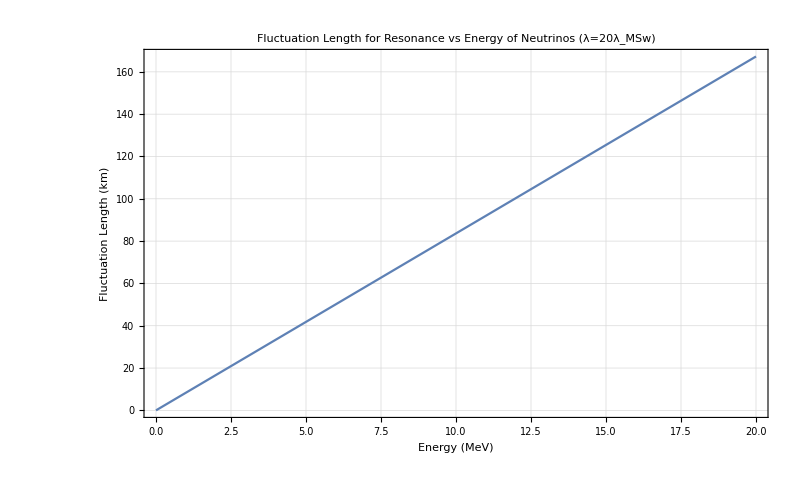

```mathematica
Plot[MeVInverse2km[1/OmegaMatter2[fraction*Cos[2thetaV]OmegaVacuum[ene,deltamsquare13],thetaV,OmegaVacuum[ene,deltamsquare13]]],{ene,0,20},Frame->True,LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImageSize->imgsize,PlotLabel->"Fluctuation Length for Resonance vs Energy of Neutrinos (λ="<>ToString[fraction]<>"λ_MSw)",FrameLabel->{"Energy (MeV)","Fluctuation Length (km)"},GridLines->Automatic,GridLinesStyle->Directive[Gray,Thin, Dashed]]
```

Dependents on Energy

```mathematica
probExRegular[energy_,endpoint_:22000]:=Module[{endpointNkmM,endpointNM,hamil,thetaVM,deltamsquare13M,omegaVM,fractionM,aNM,kNM,phiNM,thetamNM,lambdaNM,solutionM,pltExM,normDistanceM},
aNM=aN;
kNM=kN;
phiNM=phiN;
deltamsquare13M=2.6*10^(-15);(*MeV^2*)
omegaVM=deltamsquare13M/(2 energy);
thetaVM=ArcSin[√0.093/2];
fractionM=20;
lambdaNM=fraction*Cos[2thetaVM]deltamsquare13M/(2 energy10);
thetamNM=ArcTan[Sin[2thetaVM]/(Cos[2thetaVM]-(lambdaNM/omegaVM)^2)]/2;
endpointNkmM=endpoint;(*km*)
(*endpointNM=endpoint;*)

normDistanceM[xkm_]:=xkm OmegaMatter[thetamNM,thetaVM,omegaVM]10^(18)/(197) ;

hamil[xhat_]:=(aNM Sin[kNM xhat+phiNM])Sin[2thetamNM]Exp[I(-xhat-Cos[2thetamNM] aNM/kNM Cos[kNM xhat+phiNM])]/2;

(*solutionM=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hamil[normDistanceM[x]]},{Conjugate[hamil[normDistanceM[x]]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointNkmM},MaxSteps->10^6];(*Now x is distance in units of km*)
*)

solutionM=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hamil[normDistanceM[x]]},{Conjugate[hamil[normDistanceM[x]]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointNkmM},MaxSteps->10^8];

Table[{x,energy,Evaluate[Abs[psi2[x]]^2/.First@solutionM]},{x,0,endpointNkmM,10}]


(*Test results*)
(*
Plot[Evaluate[Abs[psi2[x]]^2/.solutionM],{x,0,endpointNM},ImageSize->imgsize,Frame->True,FrameLabel->{"x̂","Transition Probability"},PlotStyle->Red,PlotLabel->"Stimulated Oscillations",PlotLegends->Placed[{Style["Numerical Calculation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
*)

]
```

```mathematica
probEx[energy_,endpoint_:100000]:=Module[{endpointNkmM,endpointNM,hamil,thetaVM,deltamsquare13M,omegaVM,fractionM,aNM,kNM,phiNM,thetamNM,lambdaNM,solutionM,pltExM,normDistanceM},
aNM=aN;
kNM=kN;
phiNM=phiN;
deltamsquare13M=2.6*10^(-15);(*MeV^2*)
omegaVM=deltamsquare13M/(2 energy);
thetaVM=ArcSin[√0.093/2];
fractionM=20;
lambdaNM=fraction*Cos[2thetaVM]deltamsquare13M/(2 energy10);
thetamNM=ArcTan[Sin[2thetaVM]/(Cos[2thetaVM]-(lambdaNM/omegaVM)^2)]/2;
(*endpointNkmM=endpoint;(*km*)*)
endpointNM=endpoint;

normDistanceM[xkm_]:=xkm OmegaMatter[thetamNM,thetaVM,omegaVM]10^(18)/(197) ;

hamil[xhat_]:=(aNM Sin[kNM xhat+phiNM])Sin[2thetamNM]Exp[I(-xhat-Cos[2thetamNM] aNM/kNM Cos[kNM xhat+phiNM])]/2;

(*solutionM=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hamil[normDistanceM[x]]},{Conjugate[hamil[normDistanceM[x]]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointNkmM},MaxSteps->10^6];(*Now x is distance in units of km*)
*)

solutionM=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hamil[x]},{Conjugate[hamil[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpointNM},MaxSteps->10^6];

Table[{MeVInverse2km[x/OmegaMatter[thetamNM,thetaVM,omegaVM]],energy,Evaluate[Abs[psi2[x]]^2/.First@solutionM]},{x,0,endpoint}]


(*Test results*)
(*
Plot[Evaluate[Abs[psi2[x]]^2/.solutionM],{x,0,endpointNM},ImageSize->imgsize,Frame->True,FrameLabel->{"x̂","Transition Probability"},PlotStyle->Red,PlotLabel->"Stimulated Oscillations",PlotLegends->Placed[{Style["Numerical Calculation",FontSize->16]},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18}]
*)

]
```

```mathematica
probEx[20]
```

{{0.,20,0.},{2.08486,20,6.31847×10^-14},{4.16971,20,4.61054×10^-13},{6.25457,20,7.26767×10^-13},99994,{208482.,20,0.0000273126},{208484.,20,0.0000273134},{208486.,20,0.0000273105}}
 |  |  |  |

```mathematica
probEx[10]
```

{{0.,10,0.},{4.17793,10,9.66891×10^-13},{8.35587,10,7.58549×10^-12},{12.5338,10,1.18912×10^-11},99994,{417785.,10,0.00043824},{417789.,10,0.000438255},{417793.,10,0.000438206}}
 |  |  |  |

```mathematica
listDenPlotList=Flatten[Table[probEx[ene],{ene,5,50,1}],1]
```

$Aborted

```mathematica
(*ListDensityPlot[listDenPlotList,Mesh->None,PlotRange->{{0,20000},{5,6},Automatic},ImageSize->imgsize,PlotLegends->Automatic,PlotLabel->"Single Frequency Matter Profile"]*)
```

```mathematica
ListDensityPlot[Take[listDenPlotList,{1,Length@listDenPlotList,100}],ImageSize->imgsize,FrameLabel->{"x (km)","E (MeV)"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotLabel->"Transition Probability",PlotRange->{{1000,30000},Automatic},PlotLegends->Automatic]
```

-Graphics-

```mathematica
probExRegular[20]
```

{{0,20,0.},{10,20,7.24289×10^-12},{20,20,2.73899×10^-11},{30,20,5.59758×10^-11},{40,20,8.65261×10^-11},2191,{21960,20,1.05876×10^-10},{21970,20,7.83073×10^-11},{21980,20,4.75987×10^-11},{21990,20,2.07761×10^-11},{22000,20,3.85572×10^-12}}
 |  |  |  |

```mathematica
listDenPlotListRegular=Flatten[Table[probExRegular[ene],{ene,5,20,1}],1]
```

{{0,5,0.},{10,5,1.93789×10^-9},{20,5,7.72297×10^-9},{30,5,1.72722×10^-8},{40,5,3.04505×10^-8},35206,{21960,20,1.05876×10^-10},{21970,20,7.83073×10^-11},{21980,20,4.75987×10^-11},{21990,20,2.07761×10^-11},{22000,20,3.85572×10^-12}}
 |  |  |  |

```mathematica
listDenPlotListRegularCForm=Table[{listDenPlotListRegular[[i,1]],listDenPlotListRegular[[i,2]],ToString@CForm@listDenPlotListRegular[[i,3]]},{i,1,Length@listDenPlotListRegular}]
```

{{0,5,0.},{10,5,1.937888384937177e-9},{20,5,7.722967077232985e-9},{30,5,1.727222483644107e-8},{40,5,3.045050880689712e-8},35206,{21960,20,1.0587563058718556e-10},{21970,20,7.830732452400106e-11},{21980,20,4.7598686475960926e-11},{21990,20,2.0776051502277005e-11},{22000,20,3.855716530354212e-12}}
 |  |  |  |

```mathematica
Export["export/listDenPlotListRegular-5-20.txt",listDenPlotListRegularCForm,"Table","FieldSeparators"->" ","TextDelimiters"->""]
```

export/listDenPlotListRegular-5-20.txt

```mathematica
Export["export/listDenPlotListRegular-5-20-plt.txt",Take[listDenPlotListRegular,{1,Length@listDenPlotListRegularCForm,10}],"Table","FieldSeparators"->" "]
```

export/listDenPlotListRegular-5-20-plt.txt

```mathematica
ListDensityPlot[listDenPlotListRegular,ImageSize->imgsize,FrameLabel->{"x (km)","E (MeV)"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotLabel->"Transition Probability",PlotRange->{{0,10000},{5,10}},PlotLegends->Automatic,PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
Table[probExRegular[ene],{ene,5,10,1}]
```

{{{0,5,0.},{10,5,1.93789×10^-9},{20,5,7.72297×10^-9},{30,5,1.72722×10^-8},{40,5,3.04505×10^-8},{50,5,4.70715×10^-8},{60,5,6.69003×10^-8},{70,5,8.96616×10^-8},{80,5,1.15033×10^-7},{90,5,1.42662×10^-7},{100,5,1.72157×10^-7},2180,{21910,5,5.00726×10^-7},{21920,5,5.17762×10^-7},{21930,5,5.3139×10^-7},{21940,5,5.41411×10^-7},{21950,5,5.4769×10^-7},{21960,5,5.50127×10^-7},{21970,5,5.48693×10^-7},{21980,5,5.43399×10^-7},{21990,5,5.3432×10^-7},{22000,5,5.21591×10^-7}},4,{1}}
 |  |  |  |

```mathematica
%[[1]]
```

{{0,5,0.},{10,5,1.93789×10^-9},{20,5,7.72297×10^-9},{30,5,1.72722×10^-8},{40,5,3.04505×10^-8},2191,{21960,5,5.50127×10^-7},{21970,5,5.48693×10^-7},{21980,5,5.43399×10^-7},{21990,5,5.3432×10^-7},{22000,5,5.21591×10^-7}}
 |  |  |  |

```mathematica
testData=%
```

{{0,5,0.},{10,5,1.93789×10^-9},{20,5,7.72297×10^-9},{30,5,1.72722×10^-8},{40,5,3.04505×10^-8},2191,{21960,5,5.50127×10^-7},{21970,5,5.48693×10^-7},{21980,5,5.43399×10^-7},{21990,5,5.3432×10^-7},{22000,5,5.21591×10^-7}}
 |  |  |  |

```mathematica
testDataNew=Delete[testData,Table[{i,2},{i,1,Length@testData}]]
```

{{0,0.},{10,1.93789×10^-9},{20,7.72297×10^-9},{30,1.72722×10^-8},{40,3.04505×10^-8},{50,4.70715×10^-8},2190,{21960,5.50127×10^-7},{21970,5.48693×10^-7},{21980,5.43399×10^-7},{21990,5.3432×10^-7},{22000,5.21591×10^-7}}
 |  |  |  |

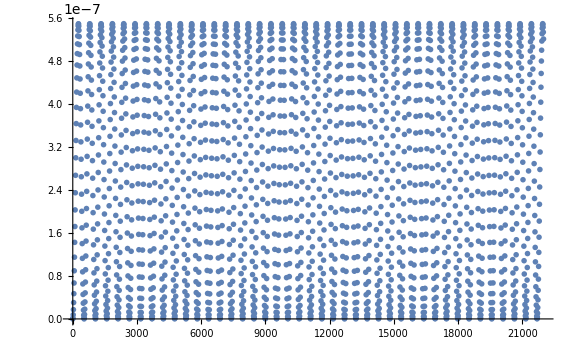

```mathematica
ListPlot[testDataNew,ImageSize->Large]
```